## FLRW and Perturbative Solutions

From Plank (2018)

```mathematica
ΩΛ=0.6847;Ωr=9.265*10^(-5);Ωm=0.3153;H0=N[67.4/3.09*10^(-19)];
```

```mathematica
H=H0*√(Ωr*a[n]^(-4)+Ωm*a[n]^(-3)+ΩΛ)
```

2.18123×10^-18 √(0.6847+0.00009265/a[n]^4+0.3153/a[n]^3)

```mathematica
HN=H/.{a[n]->ⅇ^(n)}
```

2.18123×10^-18 √(0.6847+0.00009265 ⅇ^(-4 n)+0.3153 ⅇ^(-3 n))

```mathematica
ξ=Simplify[D[HN,n]/HN]
```

(-0.000270629-0.69074 ⅇ^n)/(0.000135315+0.460494 ⅇ^n+1. ⅇ^(4 n))

#### Differential equation for F(N)=1+U+f

Numerical solution using initial conditions: F(Nini) = 0, where Nini=16 (radiation era)

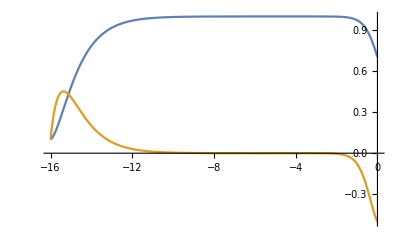

```mathematica
Nin=-16;Clear[F];Fs=NDSolve[{D[F[n],{n,2}]+(ξ+5)D[F[n],n]+(6+2ξ)F[n]==3H0^2(2/3*Ωr*ⅇ^(-4n)+Ωm*ⅇ^(-3n))/HN^2,F[Nin]==0.1,F'[Nin]==0.1},F[n],{n,Nin,0}];F=Evaluate[F[n]/.Fs[[1]][[1]]];DF=D[F,n];Plot[{F,DF},{n,0,Nin}]
```

```mathematica
(*Nin=-16;Clear[F];Fs=NDSolve[{D[F[n],{n,2}]+(ξ+5)D[F[n],n]+(6+2ξ)F[n]==-6H0^2(ΩΛ)/HN^2,F[Nin]==0,F'[Nin]==0},F[n],{n,-16,0}];F=Evaluate[F[n]/.Fs[[1]][[1]]];Plot[{F,DF},{n,0,-16}]
```

#### Differential equation for X:

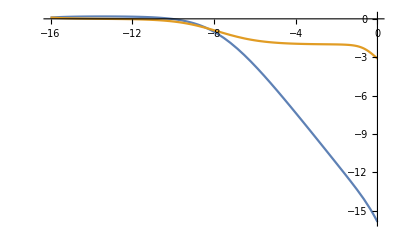

```mathematica
Clear[X];Xs=NDSolve[{D[X[n],{n,2}]+(ξ+3)D[X[n],n]==-6(2+ξ),X[Nin]==0.1,X'[Nin]==0.1},X[n],{n,Nin,0}];X2=Evaluate[X[n]/.Xs[[1]][[1]]];DX=D[X2,n];Xe=Plot[{X2,DX},{n,Nin,0}]
```

#### Differential equation for Y:

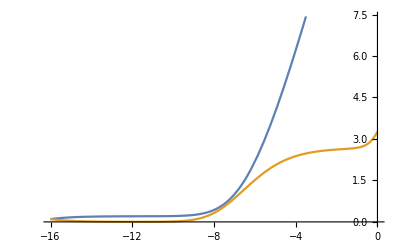

```mathematica
Clear[Y];Yn=NDSolve[{D[Y[n],{n,2}]+(ξ+3)D[Y[n],n]==DX^2,Y[Nin]==0.1,Y'[Nin]==0.1},Y[n],{n,Nin,0}];Y2=Evaluate[Y[n]/.Yn[[1]][[1]]];DY=D[Y2,n];Ye=Plot[{Y2,DY},{n,Nin,0}]
```

#### Differential equation for U and V:

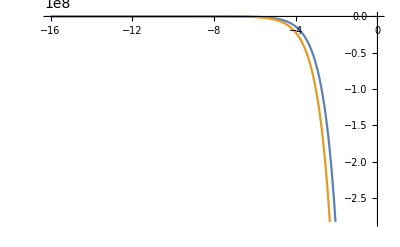

```mathematica
Vn=NDSolve[{2D[V[n],{n,2}]+2(ξ+3)D[V[n],n]+12(2+ξ)(2DX*V[n]+DF)/DY==0,V[Nin]==0.1,V'[Nin]==0.1},V[n],{n,0,Nin}];V2=Evaluate[{V[n]}/.Vn][[1]][[1]];DV=D[V2,n];Plot[{V2,DV},{n,0,Nin}]
```

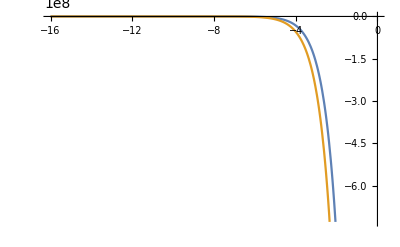

```mathematica
Un=NDSolve[{D[U[n],n]+2V2*DX==0,U[Nin]==0.1},U[n],{n,0,Nin}];U2=Evaluate[{U[n]}/.Un][[1]][[1]];DU=D[U2,n];Plot[{U2,DU},{n,0,Nin}]
```

#### Non-local distortion function

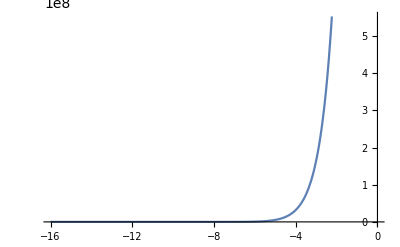

```mathematica
f=F-1-U2;Plot[f,{n,Nin,0}]
```

```mathematica
YValues=Table[Y2,{n,Nin,0,0.00025}];
```

```mathematica
Length[YValues]
```

64001

```mathematica
fValues=Table[f,{n,Nin,0,0.00025}];
```

```mathematica
Length[fValues]
```

64001

```mathematica
data=Table[{YValues[[j]],fValues[[j]]},{j,40000,64001}];
```

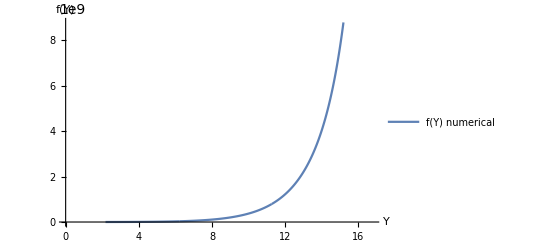

```mathematica
L=ListLinePlot[data,AxesLabel->{"Y","f(Y)"},PlotStyle->{Thick},PlotLegends->{"f(Y) numerical"}]
```

#### Exponential fit

```mathematica
fitv=FindFit[data,ⅇ^(δ(Y+β)),{β,δ},Y]
```

{β→16.1286,δ→0.732467}

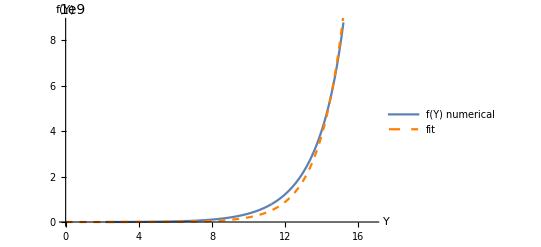

```mathematica
fit=Plot[{((ⅇ^(δ(Y+β)))/.Evaluate[fitv])},{Y,0,17},PlotStyle->{Orange,Dashed,Thick},PlotLegends->{"fit"}];S=Show[L,fit]
```

```mathematica
SetDirectory["/media/dimas/06F0EC7FF0EC75F9/Física/3 Doutorado/Papers"]
```

/media/dimas/06F0EC7FF0EC75F9/Física/3 Doutorado/Papers

```mathematica
Export["fdeY.pdf",S]
```

fdeY.pdf

```mathematica
(ⅇ^(δ(Y+β)))/.Evaluate[fitv]//TraditionalForm
```

ⅇ^(0.732467 (Y+16.1286))

#### Differential equation for δm

```mathematica
δsol=NDSolve[{D[δ[n],{n,2}]+(2+ξ)D[δ[n],n]-3/2H0^2/(ⅇ^(3n)HN^2)Ωm((F+8V2)/(F(F+6V2)))δ[n]==0,δ[-11]==0.1,δ'[-11]==0.1},δ[n],{n,-11,0}];δ2=Evaluate[{δ[n]}/.δsol][[1]][[1]]
```

InterpolatingFunction[{{-11., 0.}}, <>][n]

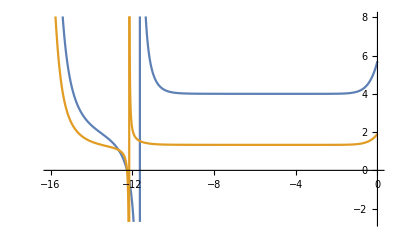

```mathematica
Plot[{(F+8V2)/(F(F+2V2)),(F+8V2)/(F(F+6V2))},{n,Nin,0}]
```

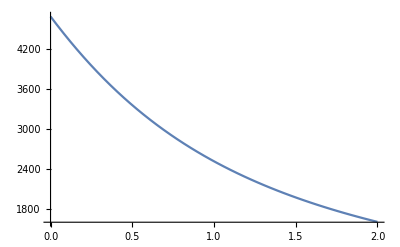

```mathematica
d1=Plot[δ2/.{n->Log[1/(1+z)]},{z,0,2}]
```

Defining growth rate fr

```mathematica
Clear[z];fr=D[Log[δ2],n];σ08=0.811;σ8=σ08*δ2/(δ2/.{n->0});fσ8DWII=fr*σ8/.{n->Log[1/(1+z)]}
```

0.000172782 InterpolatingFunction[{{-11., 0.}}, <>][Log[1/(1+z)]]

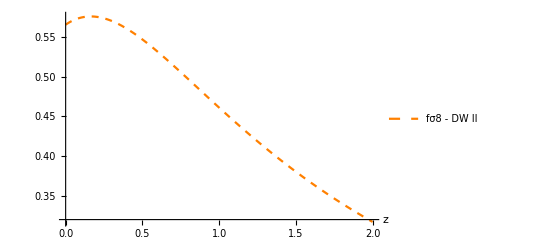

```mathematica
Pd0=Plot[{fσ8DWII},{z,0,2},PlotLegends->{"fσ8 - DW II"},LabelStyle->{Black,12},AxesLabel->{"z",""},PlotStyle->{Orange,Dashed}]
```

Comparison with ΛCDM

```mathematica
δcdm=NDSolve[{D[δ[n],{n,2}]+(2+ξ)D[δ[n],n]-3H0^2/(2ⅇ^{3n}HN^2)Ωm*δ[n]==0,δ[-16]==0.1,δ'[-16]==0.1},δ[n],{n,0,-16}];δCDM=Evaluate[{δ[n]}/.δcdm][[1]][[1]]
```

InterpolatingFunction[{{-16., 0.}}, <>][n]

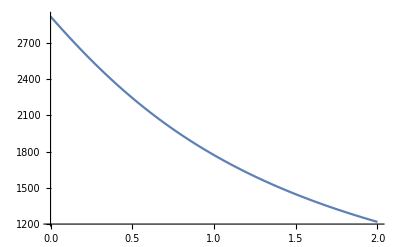

```mathematica
d2=Plot[δCDM/.{n->Log[1/(1+z)]},{z,0,2}]
```

Defining growth rate fr

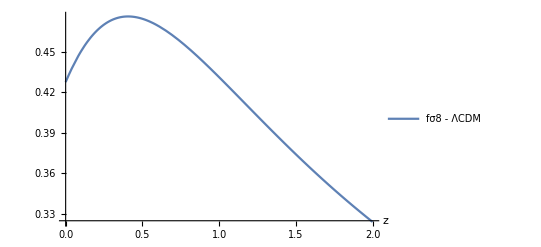

```mathematica
Clear[z];frCDM=D[Log[δCDM],n];σ08=0.811;σ8CDM=σ08*δCDM/(δCDM/.{n->0});fσ8CDM=frCDM*σ8CDM/.{n->Log[1/(1+z)]};Pd2=Plot[{fσ8CDM},{z,0,2},PlotLegends->{"fσ8 - ΛCDM"},LabelStyle->{Black,12},AxesLabel->{"z",""}]
```

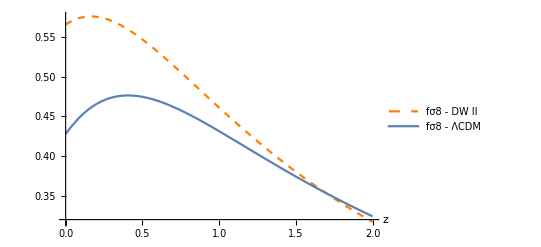

```mathematica
Show[Pd0,Pd2]
```

```mathematica
Export["fsigma8.pdf",Pd2]
```

fsigma8.pdf

#### RSD data

```mathematica
RSDdata={{0.35},{0.44±0.05},{0.77},{0.49±0.18},{0.17},{0.51±0.06},{0.02},{0.314±0.048},{0.02},{0.398±0.065},{0.25},{0.3512±0.00583},{0.37},{0.4602±0.0378},{0.25},{0.3665±0.0601},{0.37},{0.4031±0.0586},{0.44},{0.413±0.08},{0.6},{0.39±0.063},{0.73},{0.437±0.072},{0.067},{0.423±0.055},{0.3},{0.407±0.055},{0.4},{0.419±0.041},{0.5},{0.427±0.043},{0.6},{0.433±0.067},{0.8},{0.47±0.08},{0.35},{0.429±0.089},{0.18},{0.36±0.09},{0.38},{0.44±0.06},{0.32},{0.384±0.095},{0.32},{0.48±0.1},{0.57},{0.417±0.045},{0.15},{0.49±0.145},{0.1},{0.37±0.13},{1.4},{0.482±0.116},{0.59},{0.488±0.06},{0.38},{0.497±0.045},{0.51},{0.458±0.038},{0.61},{0.436±0.034},{0.38},{0.477±0.051},{0.51},{0.453±0.05},{0.61},{0.41±0.044},{0.76},{0.44±0.04},{1.05},{0.28±0.08},{0.32},{0.427±0.056},{0.57},{0.426±0.029},{0.727},{0.296±0.0765},{0.02},{0.428±0.0465},{0.6},{0.48±0.12},{0.86},{0.48±0.1},{0.6},{0.55±0.12},{0.86},{0.4±0.11},{0.1},{0.48±0.16},{0.001},{0.505±0.085},{0.85},{0.45±0.11},{0.31},{0.469±0.098},{0.36},{0.474±0.097},{0.4},{0.473±0.086},{0.44},{0.481±0.076},{0.48},{0.482±0.067},{0.52},{0.488±0.065},{0.56},{0.482±0.067},{0.59},{0.481±0.066},{0.64},{0.486±0.07},{0.1},{0.376±0.038},{1.52},{0.42±0.076},{1.52},{0.396±0.076},{0.978},{0.379±0.176},{1.23},{0.385±0.099},{1.526},{0.342±0.07},{1.944},{0.364±0.106}};
```

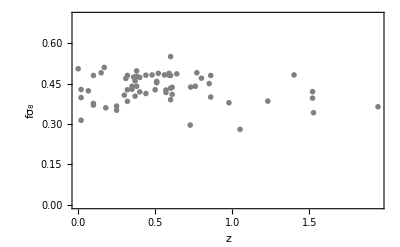

```mathematica
Do[z[k]=RSDdata[[(2k+1)]][[1]],{k,0,62,1}];Clear[fσ8];Do[fσ8[k-1]=RSDdata[[2k]][[1]][[1]],{k,1,63,1}];Do[Errf[k-1]=RSDdata[[2k]][[1]][[2]],{k,1,63,1}];RSDdata2=Table[{z[j],fσ8[j]},{j,0,125}];Ebar=Table[{Errf[k]},{k,0,62}];ListPlot[{RSDdata2},Sequence[Frame->True,FrameLabel->{"z",Subscript[fσ,8]},PlotMarkers->{"x",10}],PlotRange->{0,.7},PlotStyle->{Gray}]
```

#### Execute these lines two times!

```mathematica
datacom=Table[{RSDdata2[[k+1]],ErrorBar[Errf[k]]},{k,0,62}];
```

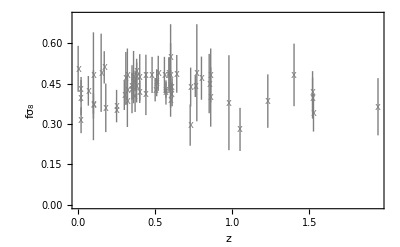

```mathematica
Needs["ErrorBarPlots`"];Pd=ErrorListPlot[datacom,Method->{"OptimizePlotMarkers"->False},Sequence[Frame->True,FrameLabel->{"z",Subscript[fσ,8]},PlotMarkers->{"x",10}],PlotRange->{0,.7},PlotStyle->{Gray,Thin}]
```

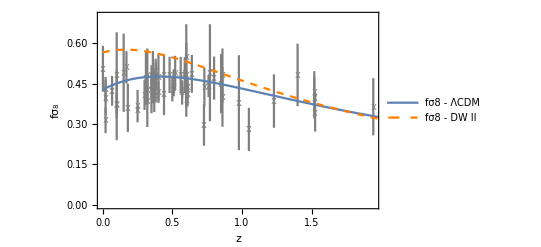

```mathematica
Show[Pd,Pd2,Pd0]
```

## I - Symmetric bounce

```mathematica
Clear["Global`*"]
```

```mathematica
SetDirectory["/media/dimas/06F0EC7FF0EC75F9/Física/3 Doutorado/Papers"]
```

/media/dimas/06F0EC7FF0EC75F9/Física/3 Doutorado/Papers

```mathematica
a=am*ⅇ^(h1*t^2/2)
```

am ⅇ^((h1 t^2)/2)

```mathematica
H=D[a,t]/a
```

h1 t

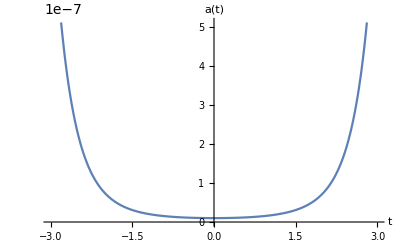

```mathematica
h1=1;am=10^(-8);pa=Plot[a,{t,-3,3},AxesLabel->{"t","a(t)"},LabelStyle->{Black,12}]
```

```mathematica
Export["aI.pdf",pa]
```

aI.pdf

#### System of ODE’s

```mathematica
simp=Simplify[{2D[H,t]F[t]+6H^2F[t]+D[F[t],{t,2}]+5H*D[F[t],t]==0,D[X[t],{t,2}]+3H*D[X[t],t]+6(D[H,t]+2H^2)==0,Y''[t]+3H*Y'[t]-D[X[t],t]^2==0,D[V[t],{t,2}]+3H*D[V[t],t]+6(D[H,t]+2H^2)(D[F[t],t]-D[U[t],t])/D[Y[t],t]==0,D[U[t],t]+2*V[t]*D[X[t],t]==0}]
```

{(2+6 t^2) F[t]+5 t F'[t]+F''[t]==0,6+12 t^2+3 t X'[t]+X''[t]==0,X'[t]^2==3 t Y'[t]+Y''[t],3 t V'[t]+(6 (1+2 t^2) (F'[t]-U'[t]))/Y'[t]+V''[t]==0,U'[t]+2 V[t] X'[t]==0}

```mathematica
Clear[F,X,Y,U,V];ti=-7;x0=0.1;sol=NDSolve[{simp,F[ti]==x0,F'[ti]==x0,X[ti]==x0,X'[ti]==x0,Y[ti]==x0,Y'[ti]==x0,V[ti]==x0,V'[ti]==x0,U[ti]==x0},{F[t],X[t],Y[t],U[t],V[t]},{t,-7,7}];L[1]="F(t)";L[2]="X(t)";L[3]="Y(t)";L[4]="U(t)";L[5]="V(t)";Do[P[i]=sol[[1]][[i]][[2]],{i,1,5}];Do[DP[i]=D[P[i],t],{i,1,5}];Table[Plot[{P[i],DP[i]},{t,-7,7},PlotLegends->{L[i],"d/dt"L[i]}],{i,1,5}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

#### Non local distortion function f(Y)

```mathematica
fp=P[1]-P[4]-1;pf=Plot[fp,{t,-7,7}, AxesLabel->{"t","f(t)"},LabelStyle->{Black,15}]
```

-Graphics-

```mathematica
YValues=Table[P[3],{t,-7,7,0.005}];fValues=Table[fp,{t,-7,7,0.005}];data=Table[{YValues[[j]],fValues[[j]]},{j,1,2801}];line=ListLinePlot[data,AxesLabel->{"Y","f(Y)"},LabelStyle->{Black,12}]
```

-Graphics-

```mathematica
Export["fYI.pdf",line]
```

fYI.pdf

#### Differential equation for δm

From Plank (2018)

```mathematica
ΩΛ=0.6847;Ωr=9.265*10^(-5);Ωm=0.3153;H0=N[67.4/3.09*10^(-19)];
```

Initial conditions δ(t = 0.1) = 0.1

```mathematica
δb=NDSolve[{D[δ[t],{t,2}]+2H*D[δ[t],t]-3H0^2/(2a^3H^2)Ωm(P[1]+8P[5])/(P[1](P[1]+2P[5]))δ[t]==0,δ[0.1]==0.1,δ'[0.1]==0.1},δ[t],{t,0.1,7}]
```

{{δ[t]→InterpolatingFunction[{{0.1, 7.}}, <>][t]}}

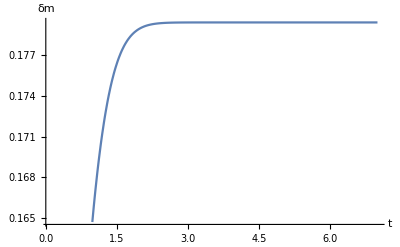

```mathematica
δb2=Evaluate[{δ[t]}/.δb][[1]][[1]];Plot[δb2,{t,0.1,7},LabelStyle->{Black,12},AxesLabel->{"t","δm"}]
```

```mathematica
Solve[a==1/(1+z),t]
```

{{t→ConditionalExpression[-√2 √(2 ⅈ π C[1]+Log[100000000/(1+z)]),C[1]∈Integers]},{t→ConditionalExpression[√2 √(2 ⅈ π C[1]+Log[100000000/(1+z)]),C[1]∈Integers]}}

```mathematica
Solve[a==1/(1+z),z]
```

{{z→-1+100000000 ⅇ^(-t^2/2)}}

```mathematica
N[(-1+100000000 ⅇ^(-t^2/2))/.{t->2}]
```

1.35335×10^7

```mathematica
N[(-1+100000000 ⅇ^(-t^2/2))/.{t->0.1}]
```

9.95012×10^7

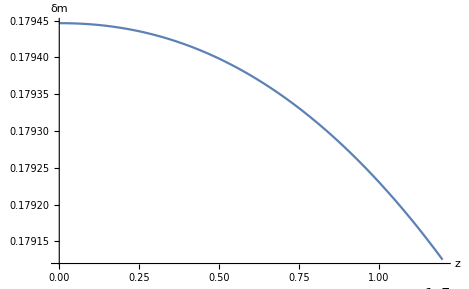

```mathematica
pδ=Plot[δb2/.{t->√2 √Log[100000000/(1+z)]},{z,0.5,1.2*10^7},LabelStyle->{Black,12},AxesLabel->{"z","δm"}]
```

```mathematica
Export["delta-m.pdf",pδ]
```

delta-m.pdf

```mathematica
dndt=D[Log[(ⅇ^(t^2/2))/100000000],t]
```

t

```mathematica
N[√2 √(+Log[100000000])]
```

6.06971

Defining growth rate

```mathematica
fr=1/t*D[Log[δb2],t];σ08=0.811;σ8=σ08*δb2/(δb2/.{t->6});fσ8DWIIb=fr*σ8
```

(4.51946 InterpolatingFunction[{{0.1, 7.}}, <>][t])/t

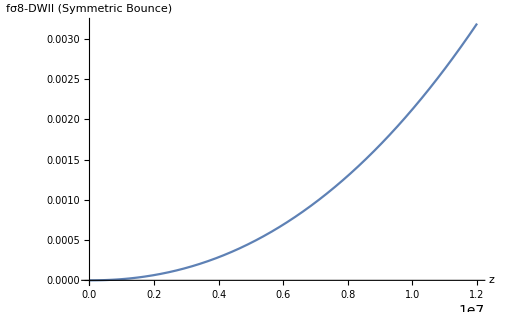

```mathematica
Plot[fσ8DWIIb/.{t->√2 √Log[100000000/(1+z)]},{z,0.5,1.2*10^7},AxesLabel->{"z","fσ8-DWII (Symmetric Bounce)"},LabelStyle->{Black,12}]
```

## II - Oscillatory Bounce

```mathematica
Clear["Global`*"]
```

```mathematica
a=A0*Sin[k*t]^2+c
```

c+A0 Sin[k t]^2

```mathematica
H=D[a,t]/a
```

(2 A0 k Cos[k t] Sin[k t])/(c+A0 Sin[k t]^2)

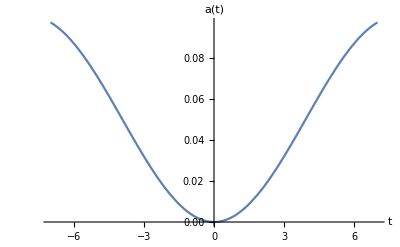

```mathematica
A0=1/10;c=10^(-8);k=3/15;pa=Plot[a,{t,-7,7},AxesLabel->{"t","a(t)"},LabelStyle->{Black,15}]
```

```mathematica
Export["aII.pdf",pa]
```

aII.pdf

#### System of ODE’s

```mathematica
simp=Simplify[{2D[H,t]F[t]+6H^2F[t]+D[F[t],{t,2}]+5H*D[F[t],t]==0,D[X[t],{t,2}]+3H*D[X[t],t]+6(D[H,t]+2H^2)==0,Y''[t]+3H*Y'[t]-D[X[t],t]^2==0,D[V[t],{t,2}]+3H*D[V[t],t]+6(D[H,t]+2H^2)(D[F[t],t]-D[U[t],t])/D[Y[t],t]==0,D[U[t],t]+2*V[t]*D[X[t],t]==0}];
```

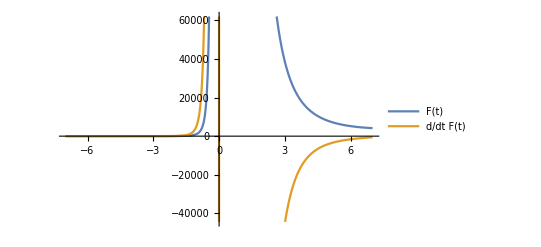
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Clear[F,X,Y,U,V];ti=-7;z=0.1;sol=NDSolve[{simp,F[ti]==z,F'[ti]==z,X[ti]==z,X'[ti]==z,Y[ti]==z,Y'[ti]==z,U[ti]==z,V[ti]==z,V'[ti]==z},{F[t],X[t],Y[t],U[t],V[t]},{t,-7,7}];L[1]="F(t)";L[2]="X(t)";L[3]="Y(t)";L[4]="U(t)";L[5]="V(t)";Do[P[i]=sol[[1]][[i]][[2]],{i,1,5}];Do[DP[i]=D[P[i],t],{i,1,5}];Table[Plot[{P[i],DP[i]},{t,-7,7},PlotLegends->{L[i],"d/dt"L[i]}],{i,1,5}]
```

#### Non local distortion function f(Y)

```mathematica
fp=P[1]-P[4]-1;pf=Plot[fp,{t,-7,7}, AxesLabel->{"t","f(t)"},LabelStyle->{Black,15}]
```

-Graphics-

```mathematica
Export["ftII.pdf",pf]
```

ftII.pdf

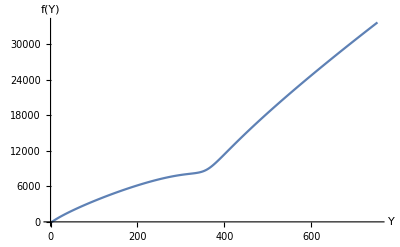

```mathematica
YValues=Table[P[3],{t,-2,2,0.005}];fValues=Table[fp,{t,-2,2,0.005}];data=Table[{YValues[[j]],fValues[[j]]},{j,1,801}];line=ListLinePlot[data,AxesLabel->{"Y","f(Y)"},LabelStyle->{Black,15}]
```

```mathematica
Export["fYII.pdf",line]
```

fYII.pdf

## III - Matter bounce

```mathematica
Clear["Global`*"]
```

```mathematica
a=A0*(3/2ρ*t^2+1)^(1/3)
```

A0 (1+(3 t^2 ρ)/2)^(1/3)

```mathematica
H=D[a,t]/a
```

(t ρ)/(1+(3 t^2 ρ)/2)

0 < ρ << 1 is a critical density from LQC

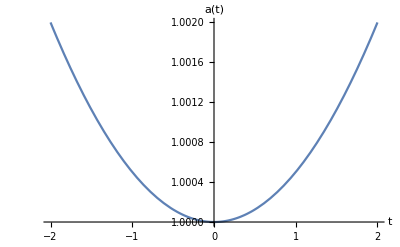

```mathematica
A0=1;ρ=10^(-3);PaI=Plot[a,{t,-2,2},AxesLabel->{"t","a(t)"},LabelStyle->{Black,15}]
```

```mathematica
Export["aIII.pdf",PaI]
```

aIII.pdf

#### System of ODE’s

```mathematica
Clear[F,X,U,V,Y]
```

```mathematica
simp=Simplify[{2D[H,t]F[t]+6H^2F[t]+D[F[t],{t,2}]+5H*D[F[t],t]==0,D[X[t],{t,2}]+3H*D[X[t],t]+6(D[H,t]+2H^2)==0,Y''[t]+3H*Y'[t]-D[X[t],t]^2==0,D[V[t],{t,2}]+3H*D[V[t],t]+6(D[H,t]+2H^2)(D[F[t],t]-D[U[t],t])/D[Y[t],t]==0,D[U[t],t]+2*V[t]*D[X[t],t]==0}]
```

{(4 F[t]+10 t F'[t]+(2000+3 t^2) F''[t])/(2000+3 t^2)==0,(12 (2000+t^2)+6 t (2000+3 t^2) X'[t]+(2000+3 t^2)^2 X''[t])/(2000+3 t^2)==0,(6 t Y'[t])/(2000+3 t^2)+Y''[t]==X'[t]^2,(12 (2000+t^2) F'[t]-12 (2000+t^2) U'[t]+(2000+3 t^2) Y'[t] (6 t V'[t]+(2000+3 t^2) V''[t]))/((2000+3 t^2) Y'[t])==0,U'[t]+2 V[t] X'[t]==0}

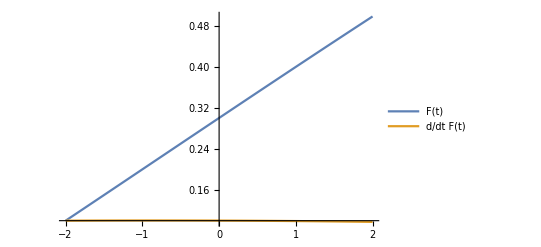
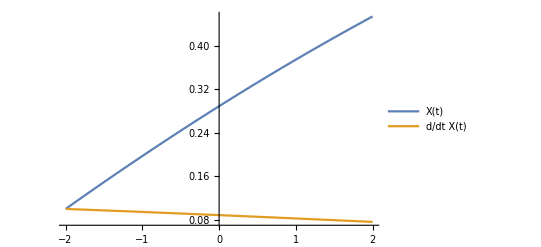
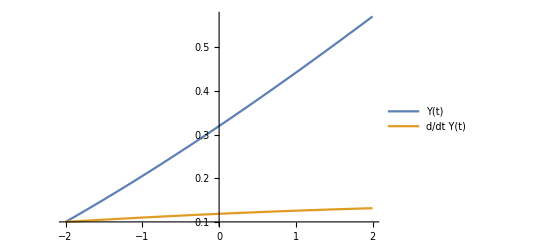
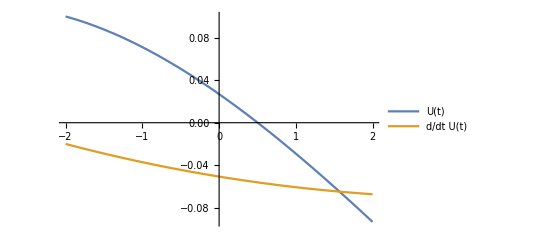
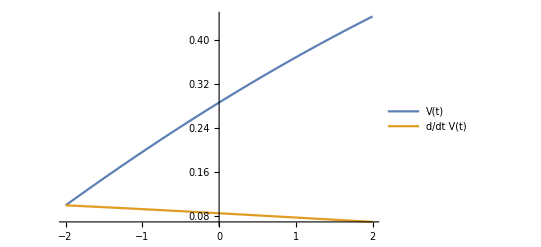

```mathematica
ti=-2;z=0.1;Clear[F,X,Y,U,V];sol=NDSolve[{simp,F[ti]==z,F'[ti]==z,X[ti]==z,X'[ti]==z,Y[ti]==z,Y'[ti]==z,V[ti]==z,V'[ti]==z,U[ti]==z},{F[t],X[t],Y[t],U[t],V[t]},{t,-2,2}];L[1]="F(t)";L[2]="X(t)";L[3]="Y(t)";L[4]="U(t)";L[5]="V(t)";Do[P[i]=sol[[1]][[i]][[2]],{i,1,5}];Do[DP[i]=D[P[i],t],{i,1,5}];Table[Plot[{P[i],DP[i]},{t,-2,2},PlotLegends->{L[i],"d/dt"L[i]}],{i,1,5}]
```

#### Non local distortion function f(Y)

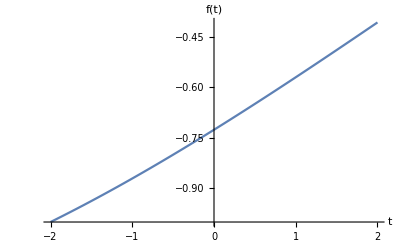

```mathematica
fp=P[1]-P[4]-1;pf=Plot[fp,{t,-2,2}, AxesLabel->{"t","f(t)"},LabelStyle->{Black,15}]
```

```mathematica
Export["ftIII.pdf",pf]
```

ftIII.pdf

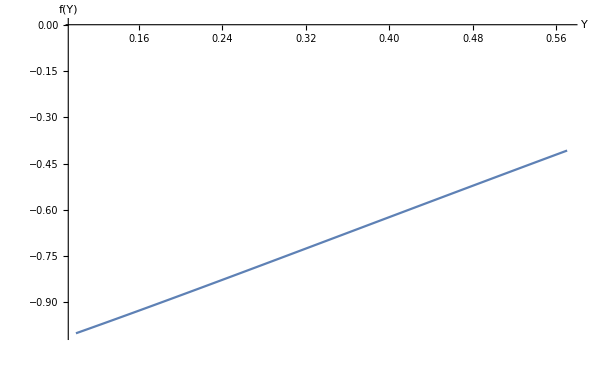

```mathematica
YValues=Table[P[3],{t,-2,2,0.005}];fValues=Table[fp,{t,-2,2,0.005}];data=Table[{YValues[[j]],fValues[[j]]},{j,1,801}];line=ListLinePlot[data,AxesLabel->{"Y","f(Y)"},LabelStyle->{Black,15}]
```

```mathematica
Export["fYIII.pdf",line]
```

fYIII.pdf

## IV - Singularities cosmologies

```mathematica
Clear[γ];a=ⅇ^(t^γ);H=D[a,t]/a;γ=3.78;D[H,{t,2}]/.{t->0}
```

0.

```mathematica
Clear["Global`*"]
```

```mathematica
a=A0*ⅇ^(f0/(α+1)*(t-ts)^(α+1))
```

A0 ⅇ^((f0 (t-ts)^(1+α))/(1+α))

```mathematica
H=D[a,t]/a
```

f0 (t-ts)^α

### α > 1

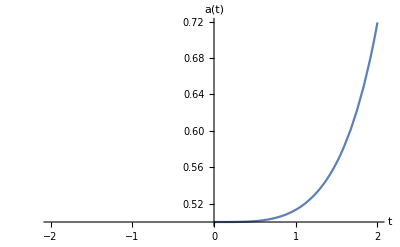

```mathematica
A0=1/2;f0=1/10;α=2.78;ts=0;pa2=Plot[{a},{t,-2,2},AxesLabel->{"t","a(t)"},LabelStyle->{Black,15}]
```

```mathematica
Export["aIV.pdf",pa2]
```

aIV.pdf

#### System of ODE’s

```mathematica
simp=Simplify[{2D[H,t]F[t]+6H^2F[t]+D[F[t],{t,2}]+5H*D[F[t],t]==0,D[X[t],{t,2}]+3H*D[X[t],t]+6(D[H,t]+2H^2)==0,Y''[t]+3H*Y'[t]-D[X[t],t]^2==0,D[V[t],{t,2}]+3H*D[V[t],t]+6(D[H,t]+2H^2)(D[F[t],t]-D[U[t],t])/D[Y[t],t]==0,D[U[t],t]+2*V[t]*D[X[t],t]==0}]
```

{3 t^2 (10+t^4) F[t]+25 (t^3 F'[t]+2 F''[t])==0,90 t^2+6 t^6+15 t^3 X'[t]+50 X''[t]==0,3/10 t^3 Y'[t]+Y''[t]==X'[t]^2,3/10 t^3 V'[t]+(3 t^2 (15+t^4) (F'[t]-U'[t]))/(25 Y'[t])+V''[t]==0,U'[t]+2 V[t] X'[t]==0}

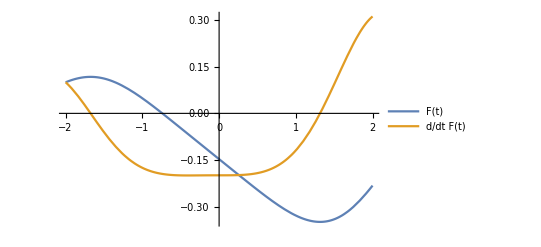
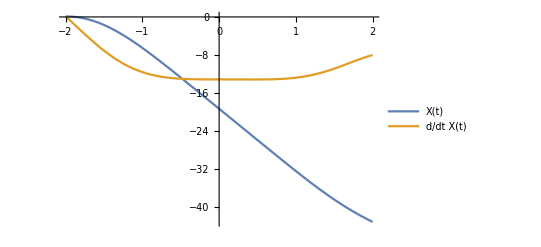
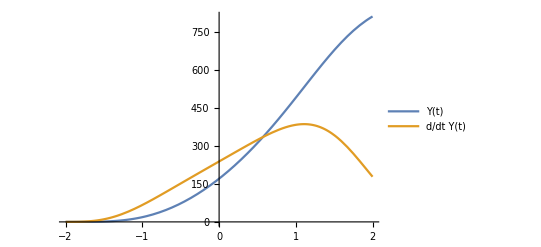
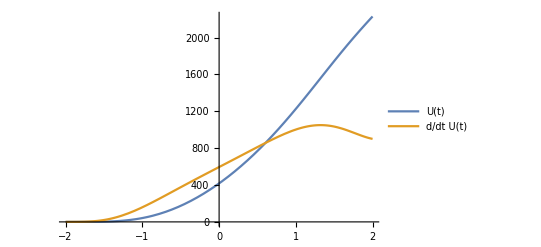
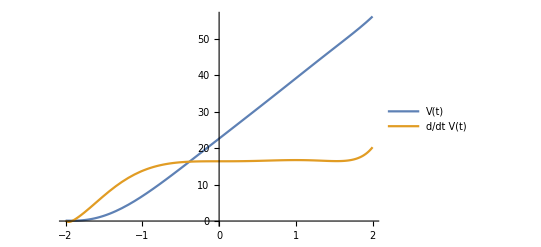

```mathematica
ti=-2;z=0.1;cc={F[ti]==z,X[ti]==z,Y[ti]==z,F'[ti]==z,X'[ti]==z,Y'[ti]==z,V[ti]==z,V'[ti]==z,U[ti]==z};Clear[F,X,Y,U,V];sol=NDSolveValue[{simp,cc},{F[t],X[t],Y[t],U[t],V[t]},{t,-2,2}];L[1]="F(t)";L[2]="X(t)";L[3]="Y(t)";L[4]="U(t)";L[5]="V(t)";Do[P[i]=sol[[i]],{i,1,5}];Do[DP[i]=D[P[i],t],{i,1,5}];Table[Plot[{P[i],DP[i]},{t,-2,2},PlotLegends->{L[i],"d/dt"L[i]}],{i,1,5}]
```

#### Non local distortion function f(Y)

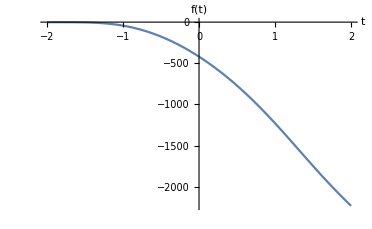

```mathematica
fp=P[1]-P[4]-1;pf=Plot[fp,{t,-2,2}, AxesLabel->{"t","f(t)"},LabelStyle->{Black,15}]
```

```mathematica
Export["ftIV.pdf",pf]
```

ftIV.pdf

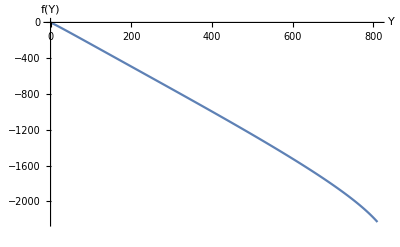

```mathematica
YValues=Table[P[3],{t,-2,2,0.005}];fValues=Table[fp,{t,-2,2,0.005}];data=Table[{YValues[[j]],fValues[[j]]},{j,1,801}];line=ListLinePlot[data,AxesLabel->{"Y","f(Y)"},LabelStyle->{Black,15}]
```

```mathematica
Export["fYIV.pdf",line]
```

fYIV.pdf

## V - Pre-inflationary asymmetric bounce

```mathematica
Clear["Global`*"]
```

```mathematica
a=a0*ⅇ^(-Hb^3*t^3-Hi^2t^2+H0*t)
```

a0 ⅇ^(H0 t-Hi^2 t^2-Hb^3 t^3)

```mathematica
H=D[a,t]/a
```

H0-2 Hi^2 t-3 Hb^3 t^2

```mathematica
Clear[H0,Hb,Hi]
```

```mathematica
Solve[D[a,t]==0,t]
```

{{t→(-Hi^2-√(3 H0 Hb^3+Hi^4))/(3 Hb^3)},{t→(-Hi^2+√(3 H0 Hb^3+Hi^4))/(3 Hb^3)}}

```mathematica
Solve[3 H0 Hb^3+Hi^4==0,H0]
```

{{H0→-Hi^4/(3 Hb^3)}}

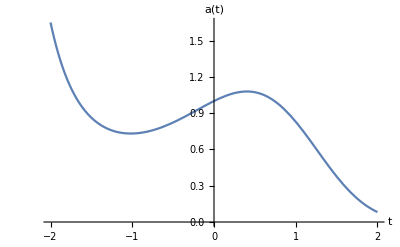

```mathematica
H0=1/3;Hi=1/2;Hb=11/17;a0=1;pa=Plot[a,{t,-2,2},AxesLabel->{"t","a(t)"},LabelStyle->{Black,15}]
```

```mathematica
Export["aV.pdf",pa]
```

aV.pdf

#### System of ODE’s

```mathematica
simp=Simplify[{2D[H,t]F[t]+6H^2F[t]+D[F[t],{t,2}]+5H*D[F[t],t]==0,D[X[t],{t,2}]+3H*D[X[t],t]+6(D[H,t]+2H^2)==0,Y''[t]+3H*Y'[t]-D[X[t],t]^2==0,D[V[t],{t,2}]+3H*D[V[t],t]+6(D[H,t]+2H^2)(D[F[t],t]-D[U[t],t])/D[Y[t],t]==0,D[U[t],t]+2*V[t]*D[X[t],t]==0}]
```

{2 (-1/2-(7986 t)/4913) F[t]+6 (-1/3+t/2+(3993 t^2)/4913)^2 F[t]+5 (1/3-t/2-(3993 t^2)/4913) F'[t]+F''[t]==0,6 (-1/2-(7986 t)/4913+2 (-1/3+t/2+(3993 t^2)/4913)^2)+3 (1/3-t/2-(3993 t^2)/4913) X'[t]+X''[t]==0,(1-(3 t)/2-(11979 t^2)/4913) Y'[t]+Y''[t]==X'[t]^2,3 (1/3-t/2-(3993 t^2)/4913) V'[t]+1/Y'[t]6 (-1/2-(7986 t)/4913+2 (-1/3+t/2+(3993 t^2)/4913)^2) (F'[t]-U'[t])+V''[t]==0,U'[t]+2 V[t] X'[t]==0}

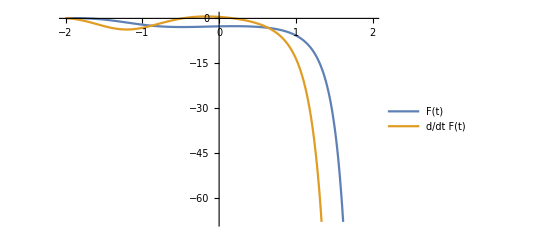
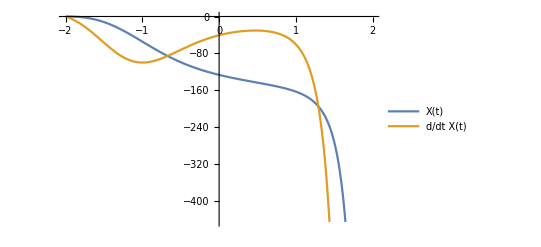
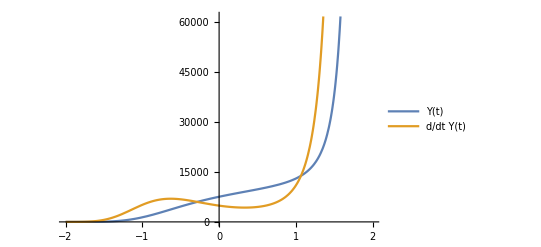
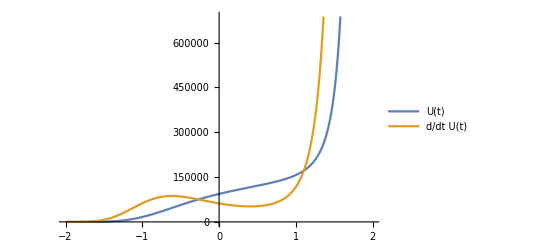
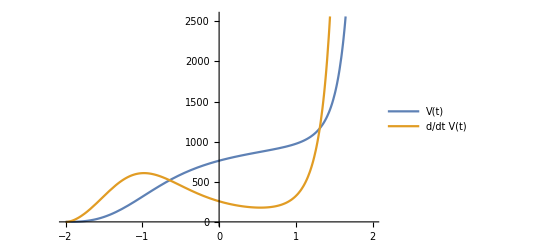

```mathematica
Clear[F,X,Y,U,V];ti=-2;z=0.1;sol=NDSolve[{simp,F[ti]==z,F'[ti]==z,X[ti]==z,X'[ti]==z,Y[ti]==z,Y'[ti]==z,V[ti]==z,V'[ti]==z,U[ti]==z},{F[t],X[t],Y[t],U[t],V[t]},{t,-2,2}];L[1]="F(t)";L[2]="X(t)";L[3]="Y(t)";L[4]="U(t)";L[5]="V(t)";Do[P[i]=sol[[1]][[i]][[2]],{i,1,5}];Do[DP[i]=D[P[i],t],{i,1,5}];Table[Plot[{P[i],DP[i]},{t,-2,2},PlotLegends->{L[i],"d/dt"L[i]}],{i,1,5}]
```

#### Non local distortion function f(Y)

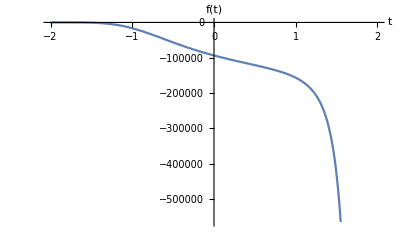

```mathematica
fp=P[1]-P[4]-1;pf=Plot[fp,{t,-2,2}, AxesLabel->{"t","f(t)"},LabelStyle->{Black,15}]
```

```mathematica
Export["ftV.pdf",pf]
```

ftV.pdf

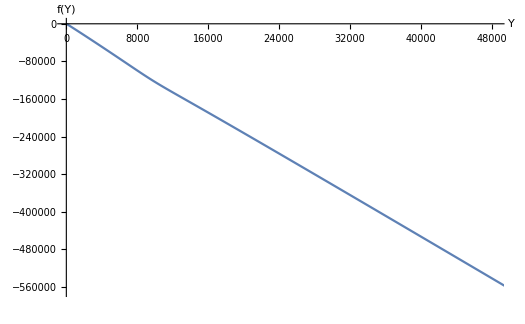

```mathematica
YValues=Table[P[3],{t,-2,2,0.005}];fValues=Table[fp,{t,-2,2,0.005}];data=Table[{YValues[[j]],fValues[[j]]},{j,1,801}];line=ListLinePlot[data,AxesLabel->{"Y","f(Y)"},LabelStyle->{Black,15}]
```

```mathematica
Export["fYV.pdf",line]
```

fYV.pdf